## Introduction

This computational essay focuses on implementation of black-box state preparation algorithm given by Grover which is widely used quantum computational primitive. Grover’s approach requires the quantum computer to calculate arc sines, a major contributer to the complexity. . The work outlines a basic three step process for state preparation executed in sequence with some modification. Preparation of the output register followed by writing target amplitudes and Amplitude transduction gives the expected amplitudes.
The task is to prepare an approximation to the ‘target’ state

target= 1/(||α(||)_2)∑_(l=0)^(d-1) α_l l

where α = (α_0, α_1,...., α_(d-1)) is a real vector with 0≤α_l≤ 1.

## Methodology

Three steps are performed:
a) Prepare the output register: Prepare out (d-dimensional quantum register) in a uniform superposition of all computational basis states 

b) Write target amplitudes: Use ‘amp’ oracle to write the target amplitude to a new n-qubit register called data controlled by the value in out. We will discuss action of ‘amp’ oracle in detail in later section.

c) Amplitude transduction: Apply the ‘rot’ oracle (implemented in later section) which performs a rotation on flag controlled by the arcsine of the value in data.

## Implementation

### Define the values

We set the precision(num), the number of data elements(dec) and the number of bits required by the index register to represent dec values. We take two random numbers({0.375,0.125} here) for the demonstration for which precision (num) is set to 3.

```mathematica
num=3;(*Precision*)
data={0.375,0.125};
Print["Data : ",data];
(*Convert to binary form*)
bin=getbin[#,num]&/@data;
Print["Binary form upto ",num," places : ",bin];
(*Convert back to decimal form*)
dec=2^num;
datan=N[FromDigits[#,2]/dec]&/@bin;
len=Length[datan];(*number of data elements*)
bitt=Ceiling[Log2[len]];(*number of bits required by the index register*)
Print["Decimal data after rounding to ",num," places : ",datan];
```

Data : {0.375,0.125}

Binary form upto 3 places : {011,001}

Decimal data after rounding to 3 places : {0.375,0.125}

### Step 1: Initialization

In the first step, the output register(out), a d-dimensional quantum register( 1-d here) starts in the 0 state. It will be later prepared in a uniform superposition of all computational basis states.

where m(len) = 2^d

```mathematica
initializer[bin_List,bitt_,len_,num_,modified_:False]:=Module[{j,k,circ},k=Floor[Log2[len]];
If[modified,j=bitt+2*num+1,j=num+2];
circ=QuantumCircuitOperator[{StringJoin[Table["I",j]],QuantumOperator["H",k]}];
circ]
```

Apply the initializer function on the above defined values

```mathematica
kk1=initializer[bin,bitt,len,num,False]
```

QuantumCircuitOperator[…]

Visualize the quantum circuit with the labels used in the convention of Grover’s state preparation algorithm.

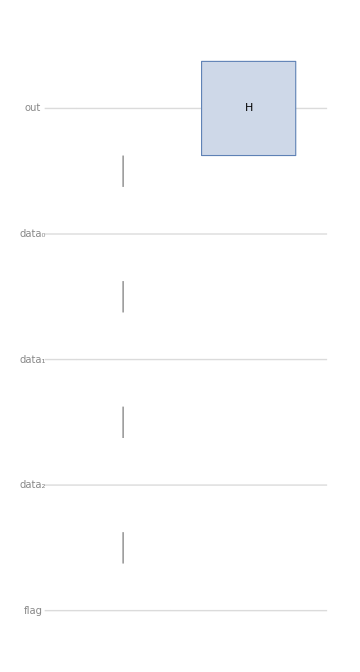

```mathematica
kk1["Diagram","WireLabels"->{"out","data_0","data_1","data_2","flag"}]
```

Find the probability of above quantum circuit. The first qubit corresponds to out register, next three corresponds to data registers and the last corresponds to flag register. Both the states are in uniform superposition state.

```mathematica
kk1[]["Probability"]
```

<|00000→1/2,10000→1/2|>

Check the amplitudes of all possible state of the above quantum circuit.

```mathematica
kk1[]["Amplitudes"]
```

<|00000→1/(√2),00001→0,00010→0,00011→0,00100→0,00101→0,00110→0,00111→0,01000→0,01001→0,01010→0,01011→0,01100→0,01101→0,01110→0,01111→0,10000→1/(√2),10001→0,10010→0,10011→0,10100→0,10101→0,10110→0,10111→0,11000→0,11001→0,11010→0,11011→0,11100→0,11101→0,11110→0,11111→0|>

### Step 2 :Apply black box amp

In second step, we use a oracle amp to write the target amplitude to data registers controlled by the value in out register. The oracle when applied on the circuit prepared the system in the following state:

where

Create the amp oracle.

```mathematica
kk2=MapIndexed[QuantumOperator[{"C",alnToGate[#1],Splice[If[OddQ@First[#2],{{},{1}},{{1},{}}]]}]&,bin]
```

{QuantumOperator[…],QuantumOperator[…]}

Create the quantum circuit operator created by the oracle. Note that the open-controlled gate are also used alternatively in the oracle

```mathematica
kk2op=QuantumCircuitOperator[kk2]
```

QuantumCircuitOperator[…]

Check the full quantum circuit until the oracle amp is used.

```mathematica
kk2o=QuantumCircuitOperator[{kk1,kk2}]
```

QuantumCircuitOperator[…]

Visualize the diagram

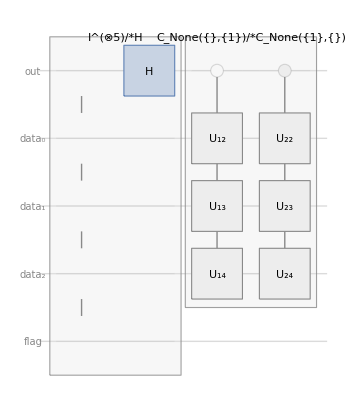

```mathematica
kk2o["Diagram","WireLabels"->{"out","data_0","data_1","data_2","flag"}]
```

Check the probability of above quantum circuit.

```mathematica
kk2o[]["Probability"]
```

<|00110→1/2,10010→1/2|>

Note the differences between probability of both of the above quantum circuit.

Find the amplitudes of quantum circuit kk20.

```mathematica
kk2o[]["Amplitudes"]
```

<|00000→0,00001→0,00010→0,00011→0,00100→0,00101→0,00110→1/(√2),00111→0,01000→0,01001→0,01010→0,01011→0,01100→0,01101→0,01110→0,01111→0,10000→0,10001→0,10010→1/(√2),10011→0,10100→0,10101→0,10110→0,10111→0,11000→0,11001→0,11010→0,11011→0,11100→0,11101→0,11110→0,11111→0|>

00110 and 10010 have equal amplitudes.

### Step 3 :Perform rotation operation

A key contributor to the cost of Grover state preparation is the use of a subroutine called rot operator. to implement this procedure, the quantum computer would calculate θ, store the value in an ancillary register (flag) and use that register as the control for a sequence of rotation operations on the qubit. When applied to the system, it results in the following state.

where

Create the rot operator of the algorithm.

```mathematica
kk3=MapIndexed[QuantumOperator[{"C",{"RY",Pi-2*ArcSin[datan[[First[#2]]]]}->{num+2},Splice[If[OddQ@First[#2],{{},{1}},{{1},{}}]]}]&,bin]
```

{QuantumOperator[…],QuantumOperator[…]}

Create the quantum circuit operator from the rot operator.

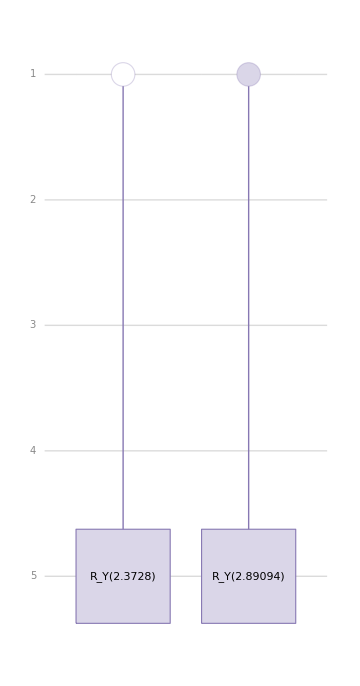

```mathematica
QuantumCircuitOperator[kk3]["Diagram"]
```

Create the overall quantum circuit.

```mathematica
kk3o=QuantumCircuitOperator[{kk1,kk2,kk3}]
```

QuantumCircuitOperator[…]

Visualize the circuit operator.

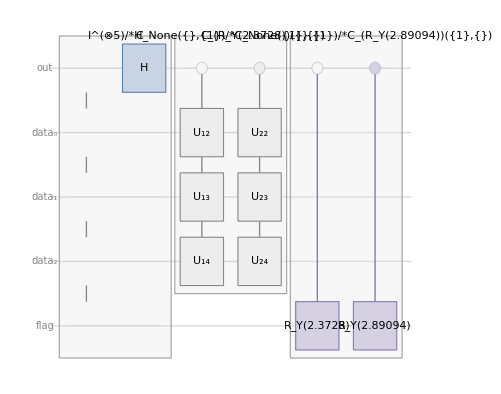

```mathematica
kk3o["Diagram","WireLabels"->{"out","data_0","data_1","data_2","flag"}]
```

Note that the open controlled gate is used alternatively.

Check the probability of the quantum circuit formed yet.

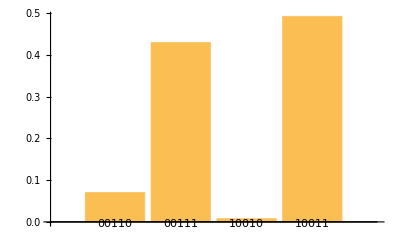

```mathematica
BarChart[kk3o[]["Probability"],ChartLabels->Automatic]
```

Similary, find the amplitudes of the output of above quantum circuit.

```mathematica
kk3o[]["Amplitudes"]
```

<|00000→0,00001→0,00010→0,00011→0,00100→0,00101→0,00110→0.265165,00111→0.655506,01000→0,01001→0,01010→0,01011→0,01100→0,01101→0,01110→0,01111→0,10000→0,10001→0,10010→0.0883883,10011→0.701561,10100→0,10101→0,10110→0,10111→0,11000→0,11001→0,11010→0,11011→0,11100→0,11101→0,11110→0,11111→0|>

### Step 4: Perform amplitude amplification

The above state now contains the target state, which has the data elements as amplitudes of the basis vectors. However the rotation also introduces some unwanted states. To eliminate these states and increase the probability of the desired state, we perform amplitude amplification on the state. After amplitude amplification, we will be left with a superposition of the desired state, and an undesired state which has a small probability. Grover prescribes roughly √d/||α(||)_2 rounds of amplitude amplification in which both amp and rot are invoked. The number of rounds of amplitude amplification, and hence the number of uses of amp oracle, is provably optimal.

#### Step 4a

Create phase oracle to be used in amplitude amplification.

```mathematica
phaseoracle[bitt_,num_,modified_:False]:=Module[{j},If[modified,j=bitt+2*num+1;
{QuantumOperator["X",{j}],QuantumOperator[{"C","Z"->{j},{},{j-1,j-2,j-3}}],QuantumOperator["X",{j}]},j=num+2;
{QuantumOperator["X",{j}],QuantumOperator["Z",{j}],QuantumOperator["X",{j}]}]]
```

Apply phase oracle function for the given input.

```mathematica
kk4a=QuantumCircuitOperator[phaseoracle[bitt,num,False]]
```

QuantumCircuitOperator[…]

Create complete quantum circuit (until phase oracle)

```mathematica
kk4ao=QuantumCircuitOperator[{kk1,kk2,kk3,kk4a}]
```

QuantumCircuitOperator[…]

Above circuit in dagger form is useful for the amplitude amplification.

```mathematica
kk4aod=QuantumCircuitOperator[kk4a]/*QuantumCircuitOperator[kk3]["Dagger"]/*QuantumCircuitOperator[kk2]["Dagger"]/*QuantumCircuitOperator[kk1]
```

QuantumCircuitOperator[…]

Visualize the complete circuit in dagger form.

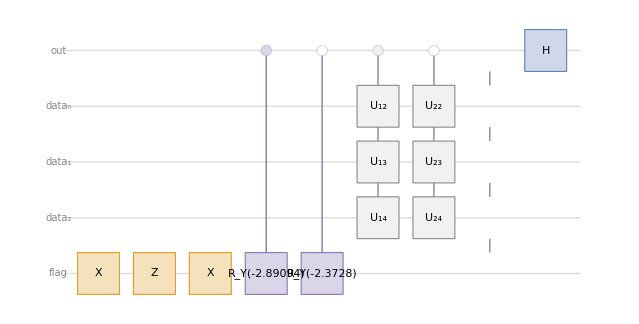

```mathematica
kk4aod["Diagram","WireLabels"->{"out","data_0","data_1","data_2","flag"}]
```

#### Step4b

Create the Grover oracle excluding Hadamard gate.

```mathematica
kk4b=QuantumCircuitOperator[{QuantumOperator["X"->Range[num+2]],QuantumOperator[{"C","Z"->num+2,Range[bitt+num]}],QuantumOperator["X"->Range[num+2]]}]
```

QuantumCircuitOperator[…]

Create the amplitude amplification oracle.

```mathematica
qq=kk4aod/*kk4b/*kk3o
```

QuantumCircuitOperator[…]

Visualize the oracle diagram.

```mathematica
qq["Diagram","WireLabels"->{"out","data_0","data_1","data_2","flag"}]
```

-Graphics-

#### Step 4c

Grover prescribes roughly √d/||α(||)_2 rounds of amplitude amplification. In this case total rounds of amplitude amplification used will be (√1)/(0.375+0.125) = 2 steps.

Concatenate all steps together (including 2 rounds of amplitude amplification)

```mathematica
fnl=kk3o/*qq/*qq
```

QuantumCircuitOperator[…]

Visualize the diagram of the whole circuit.

```mathematica
fnl["Diagram","WireLabels"->{"out","data_0","data_1","data_2","flag"}]
```

-Graphics-

Find the probability of states of above quantum circuit.

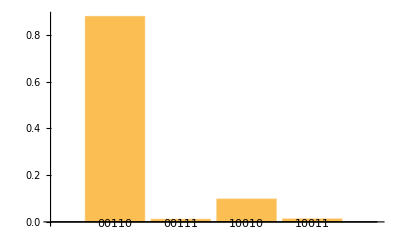

```mathematica
BarChart[fnl[]["Probability"],ChartLabels->Automatic]
```

Check the amplitudes of states of above quantum circuit.

```mathematica
fnl[]["Amplitudes"]
```

<|00000→0,00001→0,00010→0,00011→0,00100→0,00101→0,00110→0.9374,00111→0.104983,01000→0,01001→0,01010→0,01011→0,01100→0,01101→0,01110→0,01111→0,10000→0,10001→0,10010→0.312467,10011→0.112359,10100→0,10101→0,10110→0,10111→0,11000→0,11001→0,11010→0,11011→0,11100→0,11101→0,11110→0,11111→0|>

### Step 5: Unprepare qubit wire used for precision

In the last step following amplitude amplification, we reset the data register by applying the amp oracle once more.

```mathematica
kk6=fnl/*kk2op
```

QuantumCircuitOperator[…]

Check the probability and amplitudes of the complete quantum circuit (kk6)

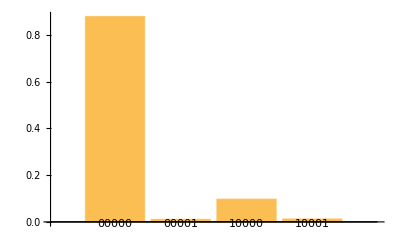

```mathematica
BarChart[kk6[]["Probability"],ChartLabels->Automatic]
```

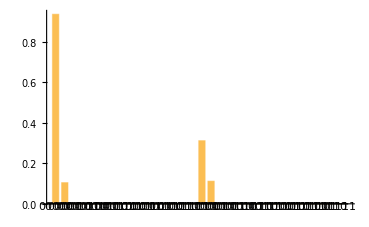

```mathematica
BarChart[kk6[]["Amplitudes"],ChartLabels->Automatic]
```

data registers can now be discarded.

#### Step 6: Measure

Finally, measure flag register. If the result is 1, the algorithm has failed. Otherwise, the state of the register out is approximately target as required.

```mathematica
kk7a=QuantumCircuitOperator[{{num+2}}];
kk7oa=kk6/*kk7a;
kk7pa=kk7oa[]["Probabilities"]
```

<|0→0.976354,1→0.0236461|>

#### Verification

To visualize the target state matching with quantum circuit, we measure the quantum circuit obtained above on the out and flag register.

```mathematica
kk7=QuantumCircuitOperator[{{bitt},{num+2}}];
kk7o=kk6/*kk7
```

QuantumCircuitOperator[…]

Check the probabilities of above quantum circuit.

```mathematica
kk7p=kk7o[]["Probabilities"]
```

<|00→0.878718,01→0.0110215,10→0.0976354,11→0.0126246|>

Check the head of keys of the probabilities obtained above.

```mathematica
Keys[kk7p][[1]]//Head
```

QuditName

Convert the probabilities to string in little endian notation.

```mathematica
keysList=Keys[kk7p];
extractedNumbers=Replace[keysList,Wolfram`QuantumFramework`QuditName[{a_Integer,b_Integer},___]:>ToString[b]<>ToString[a],{1}];
valuesList=Values[kk7p];
counts=AssociationThread[extractedNumbers->valuesList]
Head[Keys[counts][[1]]]
```

<|00→0.878718,10→0.0110215,01→0.0976354,11→0.0126246|>

String

Extract selected states whose last qubit is 0 i.e. only flag register is taken into account.

```mathematica
pp=Association@KeyValueMap[If[StringTake[#1,1]==="0",ToExpression[StringTake[#1,-1]]->#2,Nothing]&,counts]
```

<|0→0.878718,1→0.0976354|>

```mathematica
data
```

{0.375,0.125}

Coming back to the initial input provided, data variable corresponds to the probability amplitudes. It was randomly chosen. In order to check the target amplitudes, it must be normalized and further squared to see the expected probability distribution. This will be be compared with the flag register probabilities.

```mathematica
hh=AssociationThread[{0,1}->Power[Normalize[data],2]]
```

<|0→0.9,1→0.1|>

```mathematica
groupedData=Transpose[{pp[0],hh[0],pp[1],hh[1]}];
BarChart[groupedData,ChartLabels->{Automatic,{"0"," ","1"," "}},AxesLabel->{"","Probabilities"},ChartStyle->{Blue,Red,Blue,Red},ChartLegends->{"Counts","Expected"}]
```

-Graphics-

Both counts obtained and expected values obtained has higher extent of match. This shows the capability of Grover state preparation algorithm. However, this approach would require over 11000 toffoli gates per round of amplitude amplification to prepare a quantum state. Many robust algorithm has been developed recently which brings this number(toffoli gates) down to many folds.

## Initialization cells

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

Function to returns the binary form upto ‘num’ bits of precision of the input decimal data.

```mathematica
getbin[al_,num_]:=StringJoin@@ToString/@RealDigits[al,2,num,-1][[1]]
```

Function to constructs the gate that corresponds to the input binary string → X for bit ‘1’ and I for bit ‘0’.

```mathematica
alnToGate[aln_]:=Module[{xPositions,iPositions,gates},xPositions=StringPosition[aln,"1"][[All,1]];
iPositions=StringPosition[aln,"0"][[All,1]];
gates=Join[Thread["X"->xPositions],Thread["I"->iPositions]];
QuantumCircuitOperator[gates]]
```

## References

https://journals.aps.org/prl/pdf/10.1103/PhysRevLett.85.1334

https://arxiv.org/pdf/1807.03206.pdf

https://wolfr.am/wolfram-quantum

https://community.wolfram.com/groups/-/m/t/2777794

## CITE THIS NOTEBOOK

Grover's state preparation algorithm
by Shivam Sawarn
Wolfram Community, STAFF PICKS, September 6, 2023
https://community.wolfram.com/groups/-/m/t/3007057